```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants.txt","CSV"];
```

## Spectral radius of the matrix of first order moments in a process of sensitive plants and seeds

### Parameters

#### Parameters of the model

```mathematica
b= 0.9 140;
f=0.9 13000;
dZ=0.35;
gZ = 0.2;
dS=0.94;
g = 0.3;
dB=0.48;
hL=0.998;
hT=0.985;
```

```mathematica
T=b(1-dZ)gZ;
S = f(1-dS);
```

#### Parameters of the offspring distributions

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

```mathematica
λ=S g (1-hL)+T (1-hT);
λm = f(1-dS) (1-g);
```

### Spectral radius

#### Eigenvalues of the matrix of first order moments

```mathematica
φ=φ/.Solve[(λ-φ)(β-φ)-α λm==0,φ]
```

{0.095624,0.935276}

#### Spectral radius of the matrix of first order moments

```mathematica
ρ=Max[φ]
```

0.935276

## Expected number of distinct resistant lineages

#### Parameters of the model

```mathematica
A= 10^4;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
p=0.95;
dB=0.48;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
densSeeds=80;
densPlants=1;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1,2}⟧,{p,c}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Proportion of seeds that successfully establish a plant on the field

```mathematica
o=g(1-hL)/(1-(1-dB)(1-g));
```

#### Expected number of distinct resistant lineages generated by a sensitive plant

```mathematica
ν=S[[1]](M[[2,1,1]]o[[2]]+M[[3,1,1]]o[[3]])/(1-S[[1]]M[[1,1,1]]o[[1]]-T(1-hT[[1]]))
```

0.0000360505

#### Expected number of distinct resistant lineages generated by sensitive individuals

```mathematica
νtotal=ν v[[1]]A(densPlants+densSeeds o[[1]])
```

0.387713

#### Expected number of distinct resistant lineages resulting from standing variation

```mathematica
ω=A(v[[2]](densPlants+densSeeds o[[2]])+v[[3]](densPlants+densSeeds o[[3]]))
```

0.0173417

### Proportion of distinct resistant lineages generated by sensitive individuals

#### Expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕ=νtotal/ω
```

22.3573

#### Upper bound of expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕbound=ν v[[1]]/(v[[2]]+v[[3]])
```

560.997

### Number of resistant lineages resulting from standing variation and de novo mutations depending on the level of self-pollination

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{2}⟧,{c}];
v = dataStandingVariation[[Flatten[pos],{1,3,4,5}]];
```

#### Expected number of distinct resistant lineages generated by sensitive individuals

```mathematica
νtotal=ν v[[All,2]]A(densPlants+densSeeds o[[1]]);
```

#### Expected number of distinct resistant lineages resulting from standing variation

```mathematica
ω=A(v[[All,3]](densPlants+densSeeds o[[2]])+v[[All,4]](densPlants+densSeeds o[[3]]));
```

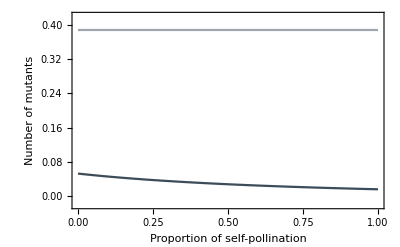

```mathematica
Show[ListPlot[{Partition[Riffle[v[[All,1]],νtotal],2],Partition[Riffle[v[[All,1]],ω],2]},PlotRange->Full,Joined->True,PlotStyle->{Directive[Lighter[RGBColor["#3C4C59"],0.5]],Directive[Lighter[RGBColor["#3C4C59"],0]]}],PlotRange->{Automatic,{-.02,.42}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Proportion of self-pollination","Number of mutants"}]
```

## Expected number of distinct resistant lineages under cross-pollination

#### Level of self-pollination

```mathematica
p=0;
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1,2}⟧,{p,c}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Proportion of seeds that successfully establish a plant on the field

```mathematica
o=g(1-hL)/(1-(1-dB)(1-g));
```

#### Expected number of distinct resistant lineages generated by a sensitive plant

```mathematica
ν=S[[1]](M[[2,1,1]]o[[2]]+M[[3,1,1]]o[[3]])/(1-S[[1]]M[[1,1,1]]o[[1]]-T(1-hT[[1]]))
```

0.0000360505

#### Expected number of distinct resistant lineages generated by sensitive individuals

```mathematica
νtotal=ν v[[1]]A(densPlants+densSeeds o[[1]])
```

0.387713

#### Expected number of distinct resistant lineages resulting from standing variation

```mathematica
ω=A(v[[2]](densPlants+densSeeds o[[2]])+v[[3]](densPlants+densSeeds o[[3]]))
```

0.0530818

### Proportion of distinct resistant lineages generated by sensitive individuals

#### Expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕ=νtotal/ω
```

7.30408

#### Upper bound of expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕbound=ν v[[1]]/(v[[2]]+v[[3]])
```

135.19

## Expected number of distinct resistant lineages under self-pollination

#### Level of self-pollination

```mathematica
p=1;
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1,2}⟧,{p,c}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Proportion of seeds that successfully establish a plant on the field

```mathematica
o=g(1-hL)/(1-(1-dB)(1-g));
```

#### Expected number of distinct resistant lineages generated by a sensitive plant

```mathematica
ν=S[[1]](M[[2,1,1]]o[[2]]+M[[3,1,1]]o[[3]])/(1-S[[1]]M[[1,1,1]]o[[1]]-T(1-hT[[1]]))
```

0.0000360505

#### Expected number of distinct resistant lineages generated by sensitive individuals

```mathematica
νtotal=ν v[[1]]A(densPlants+densSeeds o[[1]])
```

0.387713

#### Expected number of distinct resistant lineages resulting from standing variation

```mathematica
ω=A(v[[2]](densPlants+densSeeds o[[2]])+v[[3]](densPlants+densSeeds o[[3]]))
```

0.0164673

### Proportion of distinct resistant lineages generated by sensitive individuals

#### Expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕ=νtotal/ω
```

23.5444

#### Upper bound of expected proportion of distinct resistant lineages generated by sensitive individuals

```mathematica
ϕbound=ν v[[1]]/(v[[2]]+v[[3]])
```

606.704